```mathematica
Zeta[1]
```

ComplexInfinity

```mathematica
z=9.31481481481
```

9.31481

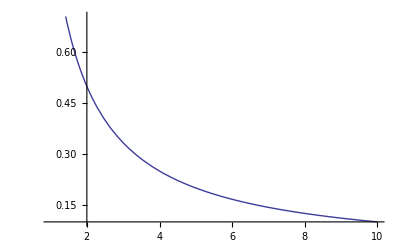

```mathematica
Plot[1/x,{x,1,10}]
```

```mathematica
1/2+1/3+1/4+1/5
```

77/60

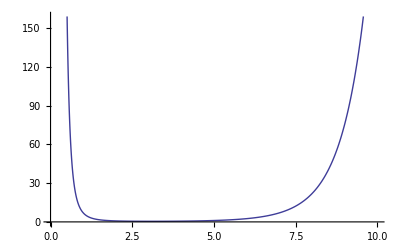

```mathematica
Plot[7^k/k^6,{k,0,10}]
```

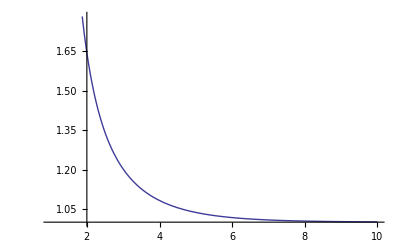

```mathematica
Plot[Zeta[k],{k,1,10}]
```

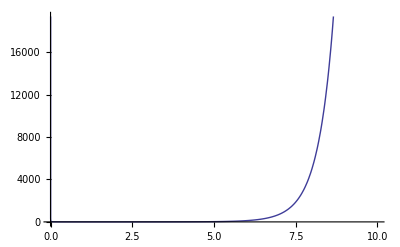

```mathematica
Plot[Gamma[k],{k,0,10}]
```

```mathematica
8!
```

40320

```mathematica
7!
```

5040

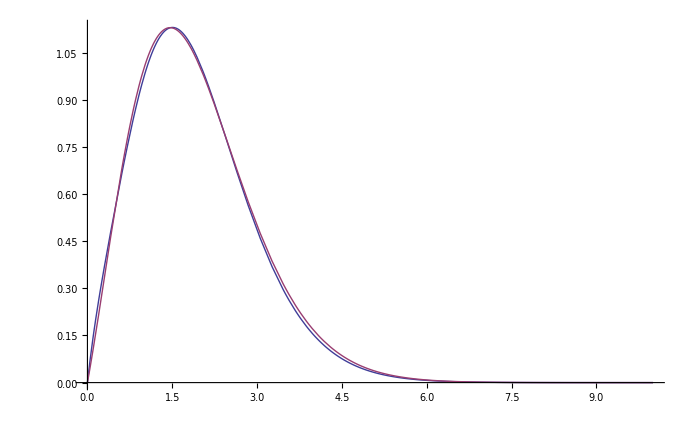

```mathematica
Plot[{(4.3x^2+7.5x^4+x^6)/( Exp[2.65x]-1),1/Gamma[x]},{x,0,10}]
```

```mathematica
Integrate[7^x/(Exp[7x]-1),x]
```

-(7^x Hypergeometric2F1[1,Log[7]/7,1+Log[7]/7,ⅇ^(7 x)])/Log[7]

```mathematica
Integrate[x Log[1-Exp[7x]],x]
```

1/49 (-7 x PolyLog[2,ⅇ^(7 x)]+PolyLog[3,ⅇ^(7 x)])

1+Log[7] x+1/2 Log[7]^2 x^2+1/6 Log[7]^3 x^3+1/24 Log[7]^4 x^4+1/120 Log[7]^5 x^5+1/720 Log[7]^6 x^6+O[x]^7

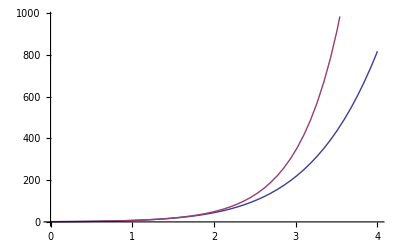

```mathematica
Series[7^x,{x,0,6}]
Plot[{1+Log[7] x+0.5Log[7]^2 x^2+1/6Log[7]^3x^3+1/24Log[7]^4 x^4+1/120 Log[7]^5 x^5+1/720 Log[7]^6 x^6,7^x},{x,0,4}]
```

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}]
```

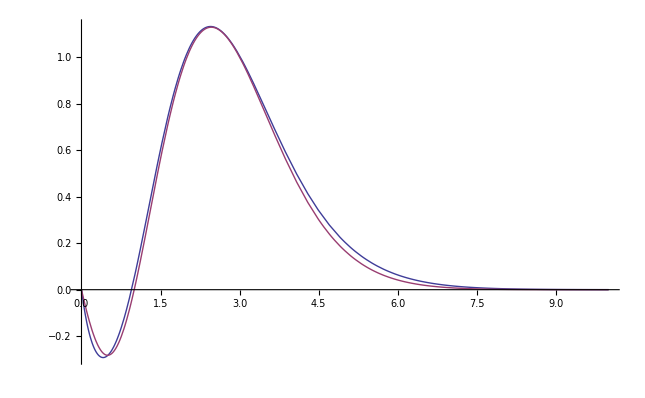

```mathematica
Plot[{(1.3x^5-1.05x)Exp[-2.08x+0.5],1/Gamma[x-1]},{x,0,10}]
```

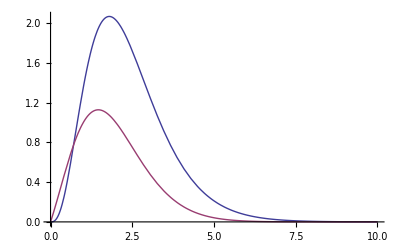

```mathematica
Plot[{(1.6x^3)Exp[-1.67x+1.5],1/Gamma[x]},{x,0,10}]
```

```mathematica
Zeta[∞]
```

1

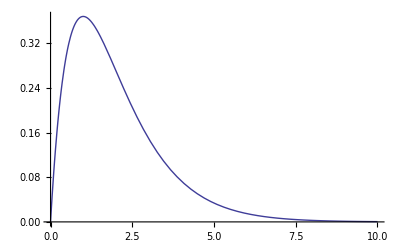

```mathematica
Plot[x Exp[-x],{x,0,10}]
```

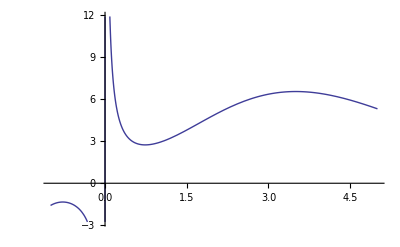

```mathematica
Plot[(1+x+x^2+x^3+x^4)/(Exp[x]-1),{x,-1,5}]
```

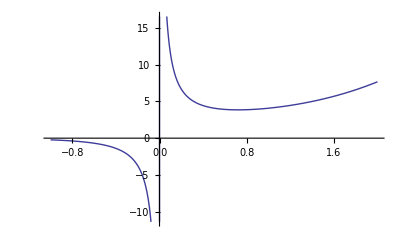

```mathematica
Plot[7^x/(Exp[x]-1),{x,-1,2}]
```

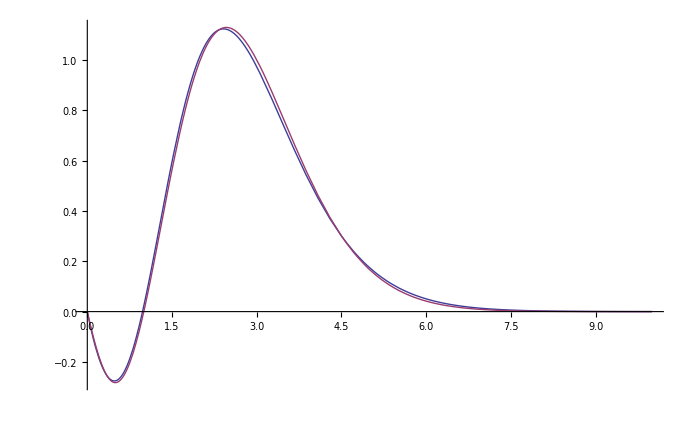

```mathematica
Plot[{(2.62x^5-2.45x^2)/(Exp[2.15x]-1),1/Gamma[x-1]},{x,0,10}]
```

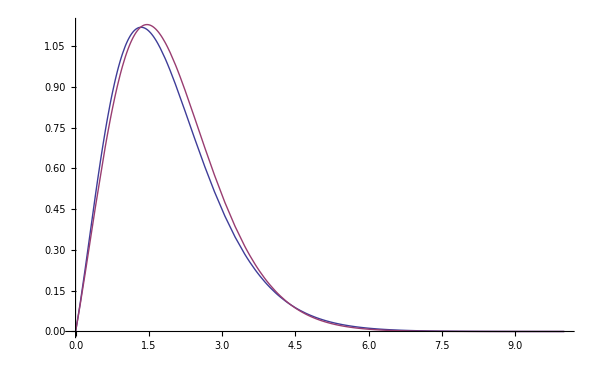

```mathematica
Plot[{(x^4+2.5x^3+3.2x^2+x)Exp[-2x],1/Gamma[x]},{x,0,10}]
```

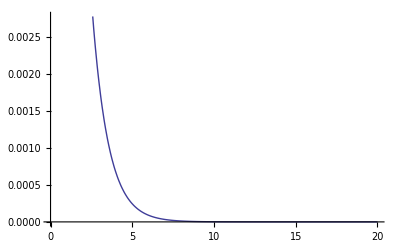

```mathematica
Plot[Log[3]^x/3^(x+3),{x,0,20}]
```

```mathematica
Plot[k^6*z^k Exp[-2.232k],{k,0,100000}]
```

-Graphics-

```mathematica
Integrate[7^k Exp[-k],k]
```

(7/ⅇ)^k/Log[7/ⅇ]

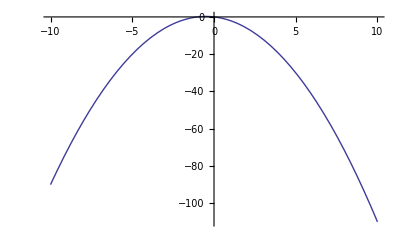

```mathematica
Plot[-x^2-x,{x,-10,10}]
```

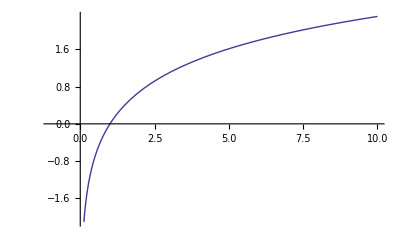

```mathematica
Plot[Log[x],{x,-1,10}]
```

```mathematica
Log[z]
```

2.23161

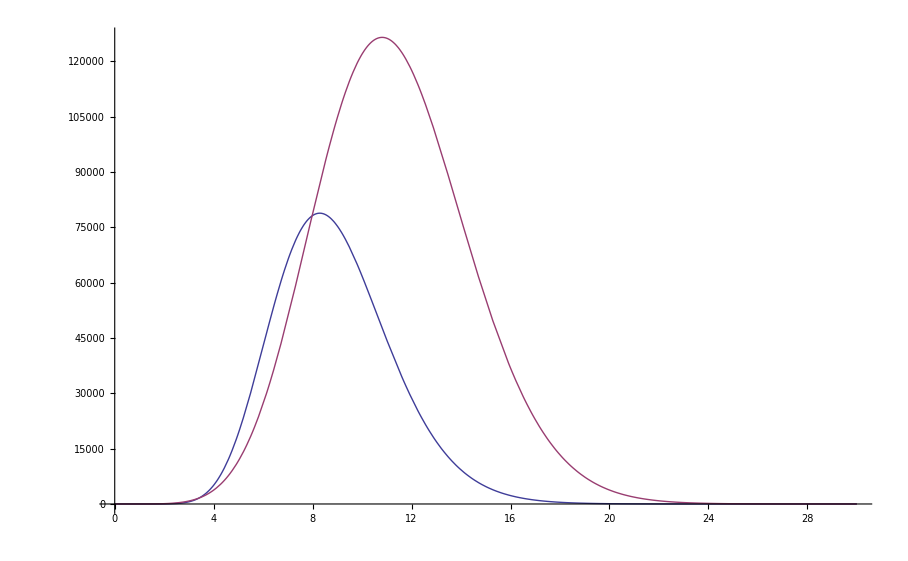

```mathematica
Plot[{z^x(0.04x^13+a12 x^12+a11 x^11+a10 x^10+a9 x^9+a8 x^8+a7 x^7+a6 x^6+a5 x^5+a4 x^4+a3 x^3+a2 x^2)/(Exp[3.8x]-1),z^x/Gamma[x-1]},{x,0,30}]
```

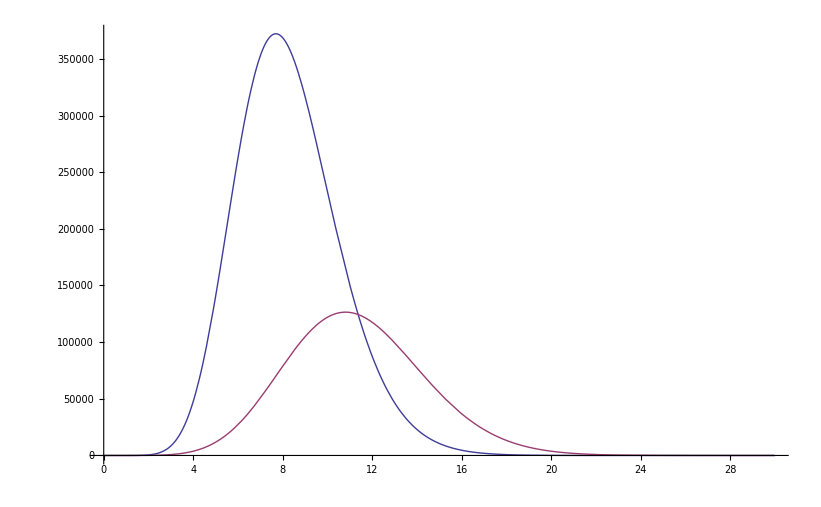

```mathematica
Plot[{z^x(0.4x^13+10x^10+x^9+x^8-x)/(Exp[3.9x]-1),z^x/Gamma[x-1]},{x,0,30}]
```

```mathematica
Integrate[(k^6+2 k^5-2.8k^2)*9.3148148^k/(Exp[2.371k]-1),{k,0,∞}]
```

7.36801×10^8

```mathematica
I1=Exp[-z]*(2/2.371^3)*NIntegrate[(k^6+2 k^5-2.8k^2)*9.3148148^k/(Exp[2.371k]-1),{k,0,∞}]
```

9958.93

```mathematica
NIntegrate[(k^6+7.5k^4+4.3k^2)*z^k/(Exp[2.65k]-1),{k,0,∞}]
```

334959.

```mathematica
D1=Exp[-z]*(2/2.371^3)*NIntegrate[(k^6+7.5k^4+4.3k^2)*z^k/(Exp[2.65k]-1),{k,0,∞}]
```

4.52745

```mathematica
D1/I1
```

0.000454613

```mathematica
NIntegrate[z^k/Gamma[k],{k,0,∞}]
D1=Exp[-z]*NIntegrate[(k^6+7.5k^4+4.3k^2)*z^k/(Exp[2.65k]-1),{k,0,∞}]
Exp[-z]*NIntegrate[z^k/Gamma[k],{k,0,∞}]
```

103406.

30.173

9.31482

```mathematica
NIntegrate[z^k/Gamma[k-1],{k,0,∞}]
I1=Exp[-z]*NIntegrate[(k^6+2 k^5-2.8k^2)*z^k/(Exp[2.371k]-1),{k,0,∞}]
Exp[-z]NIntegrate[z^k/Gamma[k-1],{k,0,∞}]
```

963210.

66370.8

86.7658

```mathematica
Expand[Product[(1+k/m),{m,1,12}]*(k^2-k)]
```

-k-(58301 k^2)/27720-(2509 k^3)/2700+(3080623 k^4)/2851200+(2457169 k^5)/1555200+(2929459 k^6)/3110400+(2091947 k^7)/6220800+(3460327 k^8)/43545600+(26741 k^9)/2073600+(1001 k^10)/691200+(689 k^11)/6220800+(377 k^12)/68428800+k^13/6220800+k^14/479001600

```mathematica
Sum[1/m,{m,1,12}]
```

86021/27720

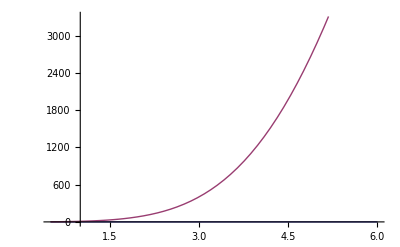

```mathematica
Plot[{((z^x x^x Exp[-x](2π x)^(1/2) )*(1+1/(12x)+1/(288x^2)-139/(51840x^3)-571/(2488320x^4)))^(-1),z^x/Gamma[x]},{x,0.5,6}]
```

```mathematica
a2=-4861/2520
a3=-29513/50400
a4=1086019/907200
a5=18491/13440
a6=100595/145152
a7=1969/9600
a8=46541/1209600
a9=187/40320
a10=253/725760
a11=1/67200
a12=1/10!
α=2.3518
```

-4861/2520

-29513/50400

1086019/907200

18491/13440

100595/145152

1969/9600

46541/1209600

187/40320

253/725760

1/67200

1/3628800

2.3518

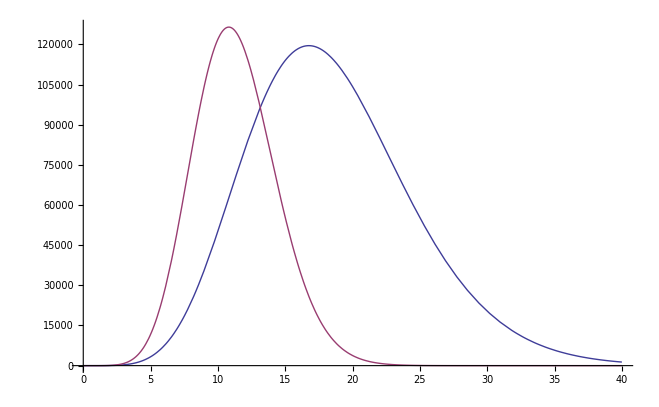

```mathematica
Plot[{(a12 x^12+a11 x^11+a10 x^10+a9 x^9+a8 x^8+a7 x^7+a6 x^6+a5 x^5+a4 x^4+a3 x^3+a2 x^2-x)z^x Exp[-(α+0.46) x],z^x/Gamma[x-1]},{x,0,40}]
```

```mathematica
NIntegrate[(a12 x^12+a11 x^11+a10 x^10+a9 x^9+a8 x^8+a7 x^7+a6 x^6+a5 x^5+a4 x^4+a3 x^3+a2 x^2-x)*z^x*Exp[-(α+0.13) x],{x,0,∞}]
Exp[-z]NIntegrate[(a12 x^12+a11 x^11+a10 x^10+a9 x^9+a8 x^8+a7 x^7+a6 x^6+a5 x^5+a4 x^4+a3 x^3+a2 x^2-x)*z^x*Exp[-(α+0.13) x],{x,0,∞}]
```

2.61348×10^10

2.35422×10^6

```mathematica
Expand[Product[(m+k),{m,1,3}]]
```

6+11 k+6 k^2+k^3

```mathematica
4*(11)
```

44

```mathematica
Expand[(k+a)*(k+b)*(k+c)*(k+d)*(k+e)]
```

a b c d e+a b c d k+a b c e k+a b d e k+a c d e k+b c d e k+a b c k^2+a b d k^2+a c d k^2+b c d k^2+a b e k^2+a c e k^2+b c e k^2+a d e k^2+b d e k^2+c d e k^2+a b k^3+a c k^3+b c k^3+a d k^3+b d k^3+c d k^3+a e k^3+b e k^3+c e k^3+d e k^3+a k^4+b k^4+c k^4+d k^4+e k^4+k^5

```mathematica
Expand[Product[(1+k/m),{m,1,50}]*(k^2-k)]
```

-k-(10844193072978058254359 k^2)/3099044504245996706400-(678627000740303630869585193281 k^3)/141096884226523794130882320000-(3515375396062321759046324662539469 k^4)/1344149976015449131094382136320000+(4124517189345108657267513722813228867 k^5)/3401368473243799873634489891020800000+(1877839525620185739084735097146494297727289 k^6)/540001258812185667938211615098462208000000+(163751391680597189539195138015097759893320103 k^7)/48255431638535740539159335817309388800000000+(7756956988774458410750297474692688948876608697 k^8)/3546774225432376929628211182572240076800000000+(1605519048402330367122294166133610717019036237 k^9)/1510604816510684051660640077759250432000000000+(20819977655720702403048987463084301291164601453 k^10)/50467933642516035362298657143320412160000000000+(1706012171135631280878886991076119424338250761 k^11)/12905024535924211167485297294573568000000000000+(33908920781374057988870650288695064224893779229 k^12)/948519303390429520810169351151157248000000000000+(1366083536479608430855647428121230768628679 k^13)/164818051722668417571430847930695680000000000+(43508711978743678054120028455263137194120811 k^14)/26091965418865507950923437310874746880000000000+(14594736375409608807816262276139495416803949 k^15)/49660395584264875381305033746074828800000000000+(199613151126808942235536026757447403776085025331 k^16)/4365446734230388135269000296482453900492800000000000+(21124534232703422085172332695299285786373 k^17)/3342313151292120854762899243385487360000000000+(255556674042705514126357136779890193855841 k^18)/327546688826627843766764125851777761280000000000+(171818435438980769747512286745478846979903 k^19)/1988676325018811908583925049814364979200000000000+(19078557767710336232686346212267271049737 k^20)/2214662271043676898195734714565997363200000000000+(5518252090361544843935444642909458641809 k^21)/7112442385949633178935449589924317102080000000000+(44110428140976426764653428309472052644373 k^22)/697019353823064051535674059812583076003840000000000+(139609328750429676509901645779061109 k^23)/29796574721196619936889189735753318400000000000+(921155177211089519792110086077773543 k^24)/2920064322677268753815140594103825203200000000000+(56316064946413471171595800174176923 k^25)/2911433590689060077695489932249331138560000000000+(23735937442511700138262554620141627 k^26)/21947730145194452893396770258494957813760000000000+(8827416987934907637804959050111 k^27)/159968878609289015257993952321391820800000000000+(47684298966521217385314179250430501 k^28)/18545831972689312694920270868428239352627200000000000+(22757639893207756165762922227 k^29)/207959542192075719835392138017809367040000000000+(228604698501971653009641963553 k^30)/53729183537261745070198586931510383738880000000000+(6932556881606706638771700781 k^31)/45886725070642794702809352193060110336000000000000+(682637693700374190152949726247 k^32)/139403870764612810307134811962516615200768000000000000+(1497577928755231404929431 k^33)/10345370743199466442087926676253552148480000000000+(127497385888547819090677 k^34)/32704720413985410042729574653962842275840000000000+(6945621412444038805087 k^35)/72728734172116549799640687536068204953600000000000+(15138926559452248051099 k^36)/7127415948867421880364787378534684085452800000000000+(2785775750016827 k^37)/65102447468646527953642559175508623360000000000+(325188311875366993 k^38)/417647224153091010636760165393774474690560000000000+(67119068749538567 k^39)/5263207365602728552412232696543994655539200000000000+(114124652031947497 k^40)/609575107616170561433925859581549926468812800000000000+(210647372053 k^41)/85929916173105772284281350147657055600640000000000+(68765937117167 k^42)/2416864822284772951267697254253002345823600640000000000+(22799926697 k^43)/78469637087167952963236923839383193046220800000000000+(20860772887 k^44)/8065147577690872043587326757540506719433523200000000000+(73632703 k^45)/3711613834223044175161106497602825031086243840000000000+(2042357 k^46)/15814702424080796920251671163698993610715299840000000000+(42649 k^47)/60976512990807154306218178174903554082131148800000000000+(861131 k^48)/280857818835657752734440928673605770102296071372800000000000+(587 k^49)/56171563767131550546888185734721154020459214274560000000000+k^50/38495197546705538137028267146871839818216804188160000000000+k^51/23872914601030908982427478937256490458695166066688000000000000+k^52/30414093201713378043612608166064768844377641568960512000000000000

```mathematica
α2=Sum[1/m,{m,1,50}]-0.577216
```

3.92199

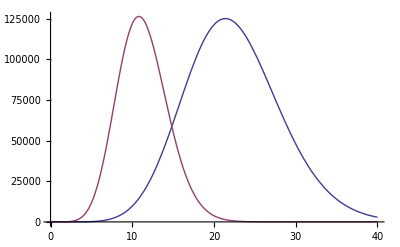

```mathematica
Plot[{(-k-(40315631 k^2)/15519504-(1165439971 k^3)/561375360+(81792623149 k^4)/213322636800+(2867680222399 k^5)/1443536640000+(1170284798881 k^6)/641571840000+(92528667701 k^7)/94058496000+(112494742951 k^8)/305690112000+(545979698191 k^9)/5349576960000+(7442796542891 k^10)/342372925440000+(1821659219 k^11)/501645312000+(2658115487 k^12)/5518098432000+(384367663 k^13)/7524679680000+(424356311 k^14)/97820835840000+(20150279 k^15)/68474585088000+(1083577 k^16)/68474585088000+(10849 k^17)/16303472640000+(14000 k^18)/69289758720000)0.009Exp[-α2 k]z^k,z^k/Gamma[k-1]},{k,0,40}]
```

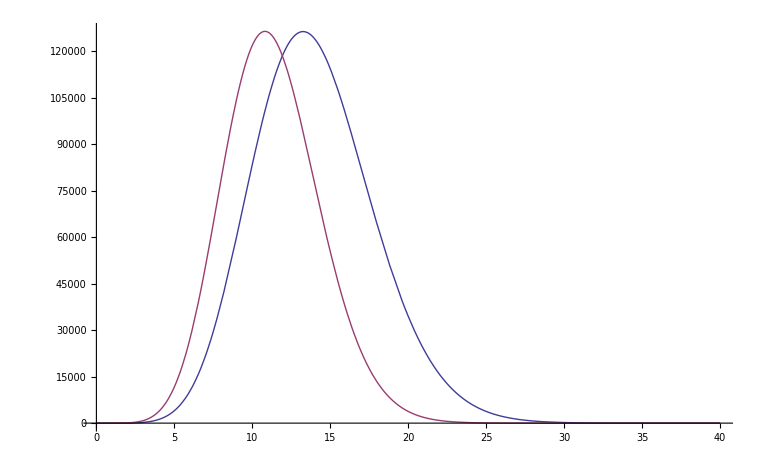

```mathematica
Plot[{(-(k+1)-(10844193072978058254359 (k+1)^2)/3099044504245996706400-(678627000740303630869585193281 (k+1)^3)/141096884226523794130882320000-(3515375396062321759046324662539469 (k+1)^4)/1344149976015449131094382136320000+(4124517189345108657267513722813228867 (k+1)^5)/3401368473243799873634489891020800000+(1877839525620185739084735097146494297727289 k^6)/540001258812185667938211615098462208000000+(163751391680597189539195138015097759893320103 k^7)/48255431638535740539159335817309388800000000+(7756956988774458410750297474692688948876608697 k^8)/3546774225432376929628211182572240076800000000+(1605519048402330367122294166133610717019036237 k^9)/1510604816510684051660640077759250432000000000+(20819977655720702403048987463084301291164601453 k^10)/50467933642516035362298657143320412160000000000+(1706012171135631280878886991076119424338250761 k^11)/12905024535924211167485297294573568000000000000+(33908920781374057988870650288695064224893779229 k^12)/948519303390429520810169351151157248000000000000+(1366083536479608430855647428121230768628679 k^13)/164818051722668417571430847930695680000000000+(43508711978743678054120028455263137194120811 k^14)/26091965418865507950923437310874746880000000000+(14594736375409608807816262276139495416803949 k^15)/49660395584264875381305033746074828800000000000+(199613151126808942235536026757447403776085025331 k^16)/4365446734230388135269000296482453900492800000000000+(21124534232703422085172332695299285786373 k^17)/3342313151292120854762899243385487360000000000+(255556674042705514126357136779890193855841 k^18)/327546688826627843766764125851777761280000000000+(171818435438980769747512286745478846979903 k^19)/1988676325018811908583925049814364979200000000000+(19078557767710336232686346212267271049737 k^20)/2214662271043676898195734714565997363200000000000+(5518252090361544843935444642909458641809 k^21)/7112442385949633178935449589924317102080000000000+(44110428140976426764653428309472052644373 k^22)/697019353823064051535674059812583076003840000000000+(139609328750429676509901645779061109 k^23)/29796574721196619936889189735753318400000000000+(921155177211089519792110086077773543 k^24)/2920064322677268753815140594103825203200000000000+(56316064946413471171595800174176923 k^25)/2911433590689060077695489932249331138560000000000+(23735937442511700138262554620141627 k^26)/21947730145194452893396770258494957813760000000000+(8827416987934907637804959050111 k^27)/159968878609289015257993952321391820800000000000+(47684298966521217385314179250430501 k^28)/18545831972689312694920270868428239352627200000000000+(22757639893207756165762922227 k^29)/207959542192075719835392138017809367040000000000+(228604698501971653009641963553 k^30)/53729183537261745070198586931510383738880000000000+(6932556881606706638771700781 k^31)/45886725070642794702809352193060110336000000000000+(682637693700374190152949726247 k^32)/139403870764612810307134811962516615200768000000000000+(1497577928755231404929431 k^33)/10345370743199466442087926676253552148480000000000+(127497385888547819090677 k^34)/32704720413985410042729574653962842275840000000000+(6945621412444038805087 k^35)/72728734172116549799640687536068204953600000000000+(15138926559452248051099 k^36)/7127415948867421880364787378534684085452800000000000+(2785775750016827 k^37)/65102447468646527953642559175508623360000000000+(325188311875366993 k^38)/417647224153091010636760165393774474690560000000000+(67119068749538567 k^39)/5263207365602728552412232696543994655539200000000000+(114124652031947497 k^40)/609575107616170561433925859581549926468812800000000000+(210647372053 k^41)/85929916173105772284281350147657055600640000000000+(68765937117167 k^42)/2416864822284772951267697254253002345823600640000000000+(22799926697 k^43)/78469637087167952963236923839383193046220800000000000+(20860772887 k^44)/8065147577690872043587326757540506719433523200000000000+(73632703 k^45)/3711613834223044175161106497602825031086243840000000000+(2042357 (k+1)^46)/15814702424080796920251671163698993610715299840000000000+(42649 (k+1)^47)/60976512990807154306218178174903554082131148800000000000+(861131 (k+1)^48)/280857818835657752734440928673605770102296071372800000000000+(587 (k+1)^49)/56171563767131550546888185734721154020459214274560000000000+(k+1)^50/38495197546705538137028267146871839818216804188160000000000+(k+1)^51/23872914601030908982427478937256490458695166066688000000000000+(k+1)^52/30414093201713378043612608166064768844377641568960512000000000000)*0.27Exp[-(α2) k]z^k,z^k/Gamma[k-1]},{k,0,40}]
```

```mathematica
Expand[Product[(1+k/m),{m,1,20}]*(k^2-k)]
```

-k-(40315631 k^2)/15519504-(1165439971 k^3)/561375360+(81792623149 k^4)/213322636800+(2867680222399 k^5)/1443536640000+(1170284798881 k^6)/641571840000+(92528667701 k^7)/94058496000+(112494742951 k^8)/305690112000+(545979698191 k^9)/5349576960000+(7442796542891 k^10)/342372925440000+(1821659219 k^11)/501645312000+(2658115487 k^12)/5518098432000+(384367663 k^13)/7524679680000+(424356311 k^14)/97820835840000+(20150279 k^15)/68474585088000+(1083577 k^16)/68474585088000+(10849 k^17)/16303472640000+(1483 k^18)/69289758720000+(13 k^19)/25583910912000+(53 k^20)/6319225995264000+k^21/11640679464960000+k^22/2432902008176640000

```mathematica
α2=Sum[1/m,{m,1,10}]-0.577215664901
α3=Sum[1/m,{m,1,20}]-0.577215664901
```

2.35175

3.02052

```mathematica
NIntegrate[(-k-(4861 k^2)/2520-(29513 k^3)/50400+(1086019 k^4)/907200+(18491 k^5)/13440+(100595 k^6)/145152+(1969 k^7)/9600+(46541 k^8)/1209600+(187 k^9)/40320+(253 k^10)/725760+k^11/67200+k^12/3628800)Exp[-α2 k]z^k,{k,0,∞}]
Exp[-z]NIntegrate[(-k-(4861 k^2)/2520-(29513 k^3)/50400+(1086019 k^4)/907200+(18491 k^5)/13440+(100595 k^6)/145152+(1969 k^7)/9600+(46541 k^8)/1209600+(187 k^9)/40320+(253 k^10)/725760+k^11/67200+k^12/3628800)Exp[-α2 k]z^k,{k,0,∞}]
```

2.06898×10^14

1.86373×10^10

```mathematica
NIntegrate[-k Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[-(4861 k^2)/2520 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[-(29513 k^3)/50400 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(1086019 k^4)/907200 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(18491 k^5)/13440 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[ (100595 k^6)/145152 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(1969 k^7)/9600 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(46541 k^8)/1209600 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(187 k^9)/40320 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[(253 k^10)/725760 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[k^11/67200 Exp[-α2 k]z^k,{k,0,∞}]
NIntegrate[ k^12/3628800 Exp[-α2 k]z^k,{k,0,∞}]
```

-69.2756

-2224.47

-16861.5

1.14762×10^6

5.48888×10^7

1.38076×10^9

2.38082×10^10

2.9739×10^11

2.68526×10^12

1.6799×10^13

6.56552×10^13

1.21436×10^14

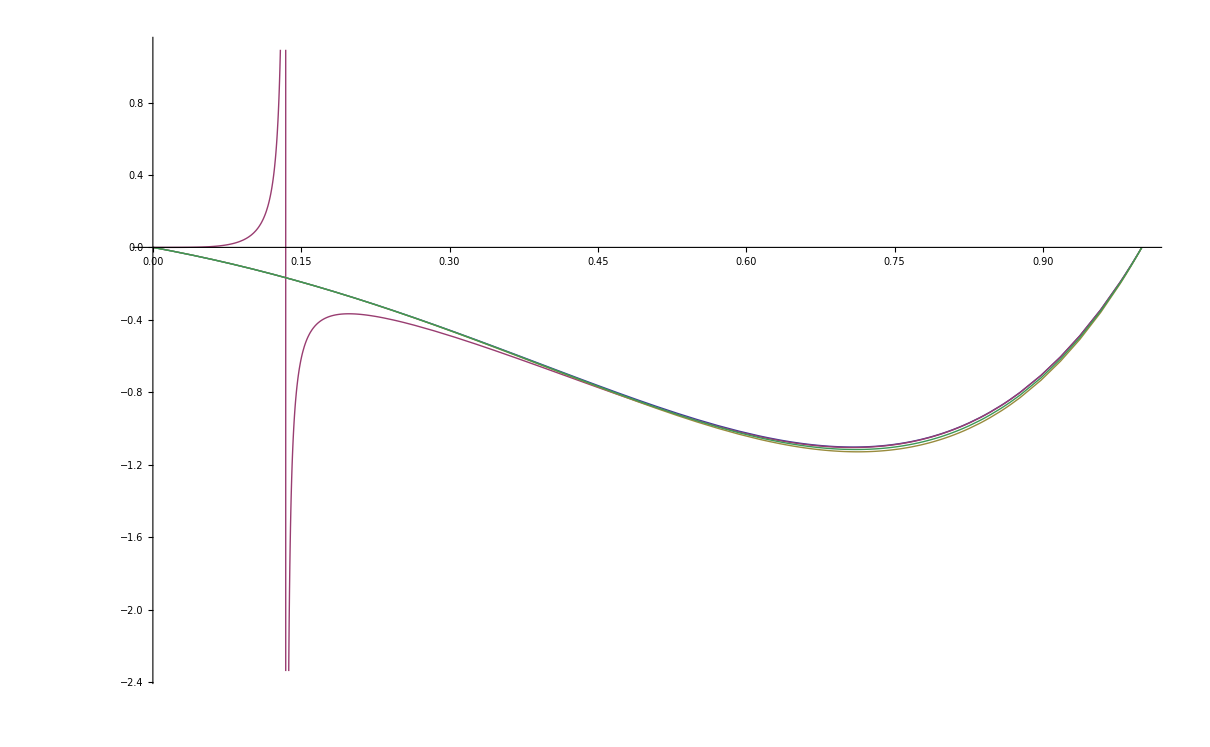

```mathematica
Plot[{z^k/Gamma[k-1],z^k(k-1)*(k^(k-1/2)Exp[-k]*(2π)^(1/2)*(1+1/(12k)+1/(288k^2)-139/(51840k^3)-571/(2488320k^4)))^(-1),(-k-(4861 k^2)/2520-(29513 k^3)/50400+(1086019 k^4)/907200+(18491 k^5)/13440+(100595 k^6)/145152+(1969 k^7)/9600+(46541 k^8)/1209600+(187 k^9)/40320+(253 k^10)/725760+k^11/67200+k^12/3628800)*Exp[-α2 k]z^k,(-k-(40315631 k^2)/15519504-(1165439971 k^3)/561375360+(81792623149 k^4)/213322636800+(2867680222399 k^5)/1443536640000+(1170284798881 k^6)/641571840000+(92528667701 k^7)/94058496000+(112494742951 k^8)/305690112000+(545979698191 k^9)/5349576960000+(7442796542891 k^10)/342372925440000+(1821659219 k^11)/501645312000+(2658115487 k^12)/5518098432000+(384367663 k^13)/7524679680000+(424356311 k^14)/97820835840000+(20150279 k^15)/68474585088000+(1083577 k^16)/68474585088000+(10849 k^17)/16303472640000+(1483 k^18)/69289758720000+(13 k^19)/25583910912000+(53 k^20)/6319225995264000+k^21/11640679464960000+k^22/2432902008176640000)Exp[-α3 k]z^k},

{k,0,1}]
```

```mathematica
Integrate[k^10Exp[-α2 k]a^k,k]
NIntegrate[k^10Exp[-α2 k]z^k,{k,0,1}]
α2
```

a^k ⅇ^(-2.35175 k) (-(3.6288×10^6 k)/(-2.35175+Log[a])^10+(1.8144×10^6 k^2)/(-2.35175+Log[a])^9-(604800. k^3)/(-2.35175+Log[a])^8+(151200. k^4)/(-2.35175+Log[a])^7-(30240. k^5)/(-2.35175+Log[a])^6+(5040. k^6)/(-2.35175+Log[a])^5-(720. k^7)/(-2.35175+Log[a])^4+(90. k^8)/(-2.35175+Log[a])^3-(10. k^9)/(-2.35175+Log[a])^2+k^10/(-2.35175+Log[a])+(3.6288×10^6)/(-2.35175+1. Log[a])^11)

0.081432

2.35175

```mathematica
0.
```

2.35175

```mathematica
2.351752253968254
```

```mathematica
dif=α2-Log[z]
pro=z Exp[-α2]
```

0.120146

0.886791

```mathematica
a11=10!*pro/dif^11
a10=10!*pro/dif^10
a9=10!*pro/(2!dif^9)
a8=10!*pro/(3!dif^8)
a7=10!*pro/(4!dif^7)
a6=10!*pro/(5!dif^6)
a5=10!*pro/(6!dif^5)
a4=10!*pro/(7!dif^4)
a3=10!*pro/(8!dif^3)
a2=10!*pro/(9!dif^2)
a1=10!*pro/(10!dif)
```

4.2733×10^16

5.13422×10^15

3.08429×10^14

1.23522×10^13

3.71019×10^11

8.91532×10^9

1.78524×10^8

```mathematica
3.0641466896579275*^6
```

46018.3

614.326

7.38091

```mathematica
1.7852399346560946*^8
```

3.06415×10^6

614.326

7.38091

```mathematica
(a1+a2+a3+a4+a5+a6+a7+a8+a9+a10+a11)
```

4.81883×10^16

```mathematica
10!/dif^11
```

4.81883×10^16

```mathematica
10!/dif^11-(a1+a2+a3+a4+a5+a6+a7+a8+a9+a10+a11)
```

```mathematica
-8.
```

```mathematica
it1=10!/dif^11-a11-a10
```

3.21161×10^14

```mathematica
it2=it1-a9-a8
```

3.80116×10^11

```mathematica
it3=it2-a7-a6
```

```mathematica
1.816347725131111*^8
```

```mathematica
it4=it3-a5-a4
```

46632.4

```mathematica
3.1107790475016534*^6
```

```mathematica
it5=it4-a3
```

614.059

```mathematica
it6=it5-a2
```

-0.267709

```mathematica
it7=it6-a1
```

-7.64862

```mathematica
-7.648621889382952
```

```mathematica
10!/dif^11-a11
```

5.45538×10^15

```mathematica
46632.35784372594-46018.2993294
```

614.059

```mathematica
46631.35784372594-46018.2993294
```

613.059

```mathematica
3.1107790475016534*^6-a4
```

46632.4

```mathematica
3.1107790475016534*^6-3.0641466896579275*^6
```

46632.4

```mathematica
46632.35784372594-a3
```

```mathematica
614.0585143614226
```

```mathematica
3.0641464219484855*^6
```

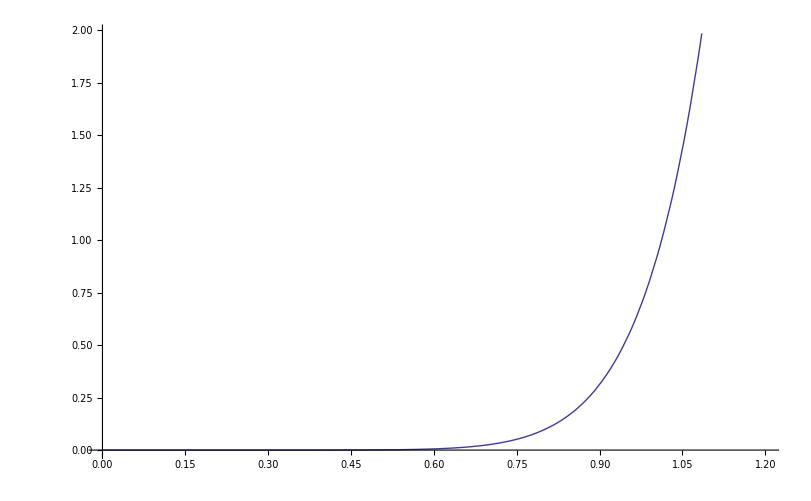

```mathematica
Plot[k^10Exp[-α2 k]z^k,{k,0,1.2}]
```

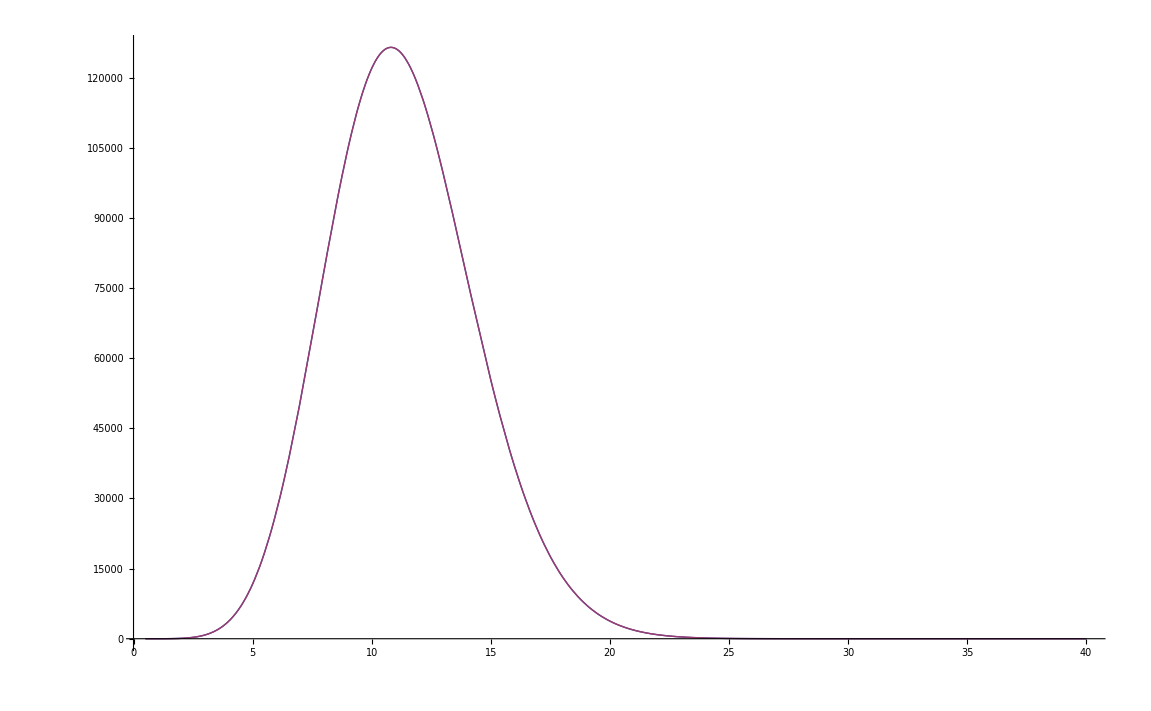

```mathematica
Plot[{z^k/Gamma[k-1],z^k(k-1)*(k^(k-1/2)Exp[-k]*(2π)^(1/2)*(1+1/(12k)+1/(288k^2)-139/(51840k^3)-571/(2488320k^4)))^(-1)},{k,0.5,40}]
```

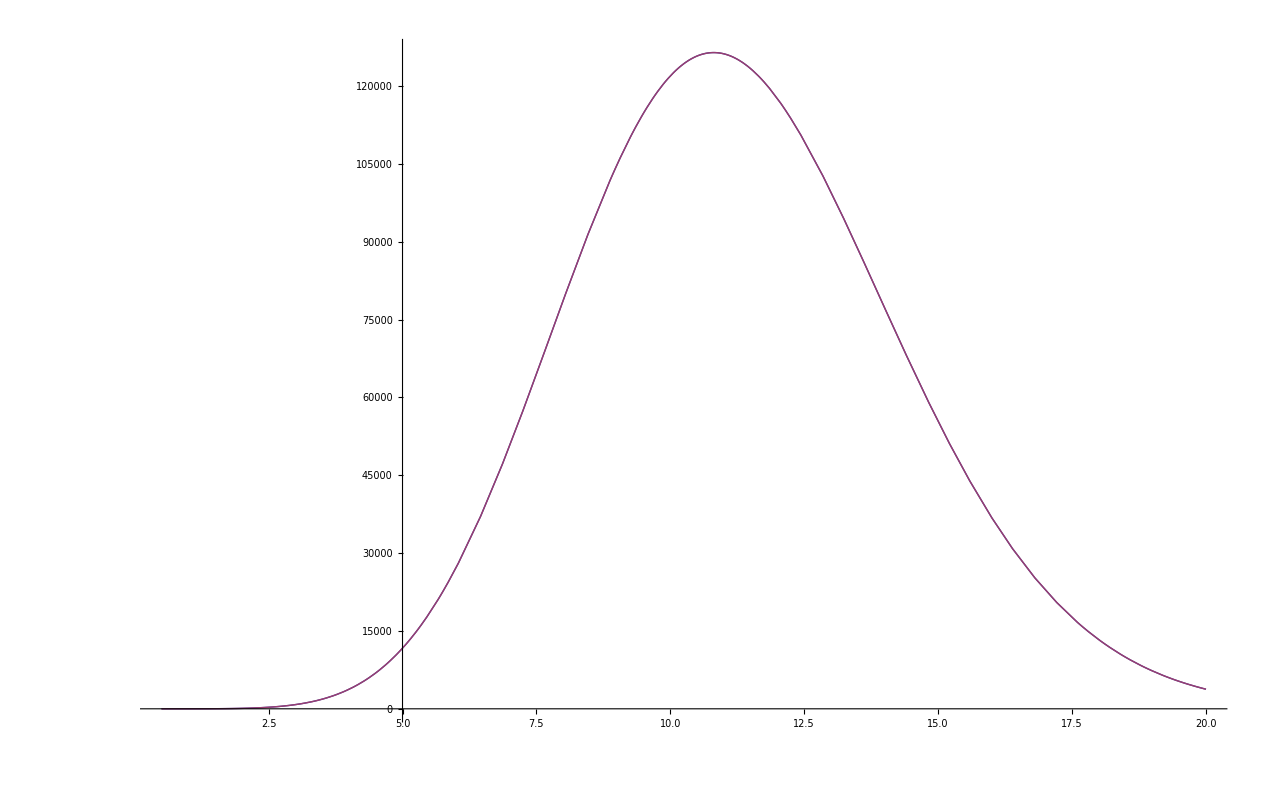

```mathematica
Plot[{z^k(k-1)*(k^(-k+1/2))Exp[k]*(2π)^(-1/2)*(1+1/(12k))^-1,z^k/Gamma[k-1]},{k,0.5,20}]
```

```mathematica
Integrate[k^-k*Exp[k],k]
```

∫ⅇ^k k^-kⅆk

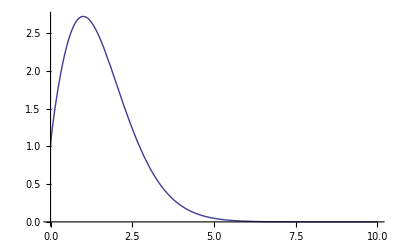

```mathematica
Plot[k^-k Exp[k],{k,0,10}]
```

```mathematica
Integrate[x^n Exp[x],x]
```

(-x)^-n x^n Gamma[1+n,-x]

```mathematica
D[Log[z x],x]
```

```mathematica
1./x
Log[x Exp[1]]
```

1./x

Log[ⅇ x]

```mathematica
Integrate[-Log[x Exp[1]],x]
```

x-x Log[ⅇ x]

```mathematica
D[x^x,x]
```

x^x (1+Log[x])

```mathematica
Log[1]
```

0

```mathematica
Series[(a Exp[1])^t,{t,0,4}]
```

1+(1+Log[a]) t+(1/2+Log[a]+Log[a]^2/2) t^2+1/6 (1+3 Log[a]+3 Log[a]^2+Log[a]^3) t^3+1/24 (1+4 Log[a]+6 Log[a]^2+4 Log[a]^3+Log[a]^4) t^4+O[t]^5

```mathematica
Series[t^(-t+a),{t,0,4}]
```

t^a (1-Log[t] t+1/2 Log[t]^2 t^2-1/6 Log[t]^3 t^3+1/24 Log[t]^4 t^4+O[t]^5)

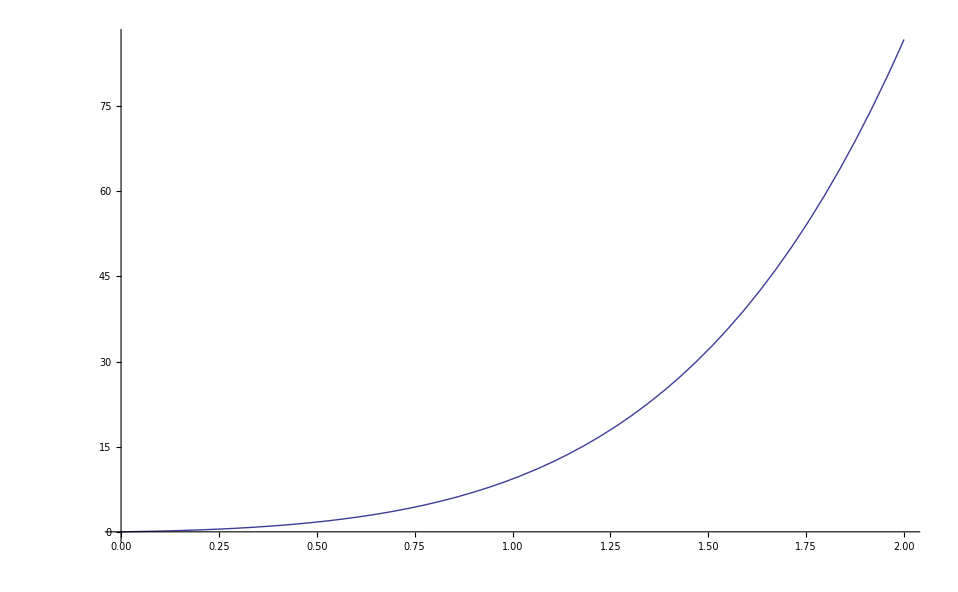

```mathematica
Plot[z^k*k/Gamma[k+1],{k,0,2}]
```